# Analyzing Economic Trends: A Comparative Study of Non-Linear Models,State-Space Models and Neural Networks

Muhammad Ali Hafeez

This computational essay explores the predictive accuracy of three models: non-linear model fits, state space models, and neural nets. The essay takes you on a journey from simple modeling techniques to discover the advantages of these techniques in a world where neural nets are gaining popularity. It is important to note that these modeling techniques are often used in conjunction with each other. However, for the purpose of comparing the models, they will be considered independently.

## Introduction

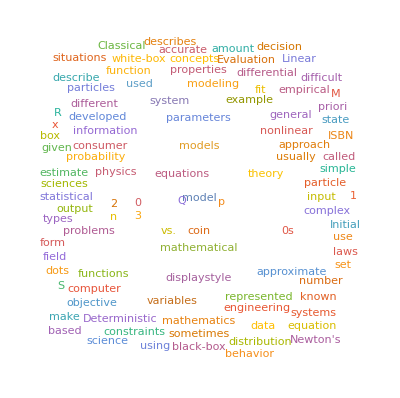

```mathematica
WordCloud[WikipediaData["Mathematical Modeling"]]
```

The purpose of this essay is to introduce a highly significant discussion. The emergence of machine learning has brought about groundbreaking advancements. However, have we thoroughly analyzed each technique in terms of their predictive power relative to one another? This essay aims to compare two crucial techniques: State-Space Models, specifically those employing the Kalman filter, and Neural Networks, which represent a more contemporary approach.

## Data

The data that will be used in this computational essay is the Federal Reserve of Economic Data (FRED) Real Gross Domestic Product data from 1947 to 2023.

```mathematica
data=Import["C:\\Users\\ali12\\Downloads\\GDP.xls"];
preprocessedData=data/. Null->"";
Dataset[preprocessedData]
```

```mathematica
gDPdataIcon=Iconize[preprocessedData,"GDPData"]
```

## Splitting the Data into Train and Test Sets

In this context, we will employ Mathematica to partition the dataset into separate testing and training sets. This division serves the purpose of evaluating the predictive capabilities of our models and safeguarding against the occurrence of overfitting.

```mathematica
whole=preprocessedData;
{trainer,tester}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole,11],Shuffle->False];
Take[Dataset[trainer],10]
Take[Dataset[tester],10]
```

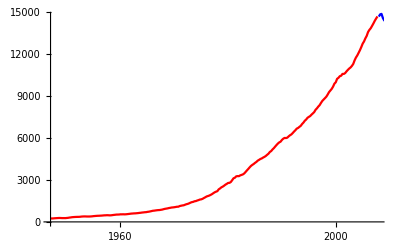

```mathematica
Show[ListLinePlot[TimeSeries[trainer],PlotStyle->Red],ListLinePlot[TimeSeries[tester],PlotStyle->Blue]]
```

## Adjustments to the Data (Relative Time)

The rationale behind implementing the additional adjustments stemmed from the challenges encountered when employing date objects for manipulations, computations, as well as the utilization of specific functions designed for non-linear model fitting and neural networks in Mathematica. In order to address these issues, a modification was made to the scale of the x-axis, which now represents relative time. The initial date in the dataset serves as the reference point, and the new x-axis values are calculated by subtracting the start date from the date in question.

```mathematica
TrainreferenceDate=DateObject[{1947,1,1,0,0,0},TimeZone->-4];
Trainedited=trainer/. Rule[a_,b_]:>{a,b};
Trainlist=Trainedited;
TrainlistWithYearsSince=Map[{#,-1*QuantityMagnitude@DateDifference[#[[1]],TrainreferenceDate,"Year"]}&,Trainlist];
Trainnewflattenedlist=Flatten[#,1]&/@ TrainlistWithYearsSince;
TrainnewList=Rest/@Trainnewflattenedlist;
TrainReveresedNewTrainList=Reverse/@TrainnewList;
TrainrefDiff=TableForm[TrainReveresedNewTrainList,TableHeadings->{None,{"Row","Date","Values","Years Since"}}];
Trainrules=TrainReveresedNewTrainList/. {a_,b_}:>Rule[a,b];
splitData3=Partition[Flatten[Trainrules],2];
table3=Grid[splitData3,Alignment->Center]//DisplayForm;
styledTable3=StyleBox[table3,GridBoxOptions->{GridBoxDividers->{"Columns"->True},GridBoxItemStyle->{"ColumnBands"->{{1,1}->Bold},"Columns"->{2->Bold}}}];
scrollableTable3=Pane[styledTable3,ImageSize->{Automatic,300},Scrollbars->True];
scrollableTable3


TestreferenceDate=DateObject[{1947,1,1,0,0,0},TimeZone->-4];
Testedited=tester/. Rule[a_,b_]:>{a,b};
Testlist=Testedited;
TestlistWithYearsSince=Map[{#,-1*QuantityMagnitude@DateDifference[#[[1]],TestreferenceDate,"Year"]}&,Testlist];
Testnewflattenedlist=Flatten[#,1]&/@ TestlistWithYearsSince;
TestnewList=Rest/@Testnewflattenedlist;
TestReveresedNewTrainList=Reverse/@TestnewList;
TestrefDiff=TableForm[TestReveresedNewTrainList,TableHeadings->{None,{"Row","Date","Values","Years Since"}}];
Testrules=TestReveresedNewTrainList/. {a_,b_}:>Rule[a,b];
splitData4=Partition[Flatten[Testrules],2];
table4=Grid[splitData4,Alignment->Center]//DisplayForm;
styledTable4=StyleBox[table4,GridBoxOptions->{GridBoxDividers->{"Columns"->True},GridBoxItemStyle->{"ColumnBands"->{{1,1}->Bold},"Columns"->{2->Bold}}}];
scrollableTable4=Pane[styledTable4,ImageSize->{Automatic,300},Scrollbars->True];
scrollableTable4
```

StyleBox[0→243.164 | 0.245902→245.968
0.494536→249.585 | 0.745902→259.745
1→265.742 | 1.2459→272.567
1.49454→279.196 | 1.7459→280.366
2→275.034 | 2.2459→271.351
2.49454→272.889 | 2.7459→270.627
3→280.828 | 3.2459→290.383
3.49454→308.153 | 3.7459→319.945
4→336. | 4.2459→344.09
4.49454→351.385 | 4.7459→356.178
5→359.82 | 5.2459→361.03
5.49454→367.701 | 5.7459→380.812
6→387.98 | 6.2459→391.749
6.49454→391.171 | 6.7459→385.97
7→385.345 | 7.2459→386.121
7.49454→390.996 | 7.7459→399.734
8→413.073 | 8.2459→421.532
8.49454→430.221 | 8.7459→437.092
9→439.746 | 9.2459→446.01
9.49454→451.191 | 9.7459→460.463
10→469.779 | 10.2459→472.025
10.4945→479.49 | 10.7459→474.864
11→467.54 | 11.2459→471.978
11.4945→485.841 | 11.7459→499.555
12→510.33 | 12.2459→522.653
12.4945→525.034 | 12.7459→528.6
13→542.648 | 13.2459→541.08
13.4945→545.604 | 13.7459→540.197
14→545.018 | 14.2459→555.545
14.4945→567.664 | 14.7459→580.612
15→594.013 | 15.2459→600.366
15.4945→609.027 | 15.7459→612.28
16→621.672 | 16.2459→629.752
16.4945→644.444 | 16.7459→653.938
17→669.822 | 17.2459→678.674
17.4945→692.031 | 17.7459→697.319
18→717.79 | 18.2459→730.191
18.4945→749.323 | 18.7459→771.857
19→795.734 | 19.2459→804.981
19.4945→819.638 | 19.7459→833.302
20→844.17 | 20.2459→848.983
20.4945→865.233 | 20.7459→881.439
21→909.387 | 21.2459→934.344
21.4945→950.825 | 21.7459→968.03
22→993.337 | 22.2459→1009.02
22.4945→1029.96 | 22.7459→1038.15
23→1051.2 | 23.2459→1067.38
23.4945→1086.06 | 23.7459→1088.61
24→1135.16 | 24.2459→1156.27
24.4945→1177.68 | 24.7459→1190.3
25→1230.61 | 25.2459→1266.37
25.4945→1290.57 | 25.7459→1328.9
26→1377.49 | 26.2459→1413.89
26.4945→1433.84 | 26.7459→1476.29
27→1491.21 | 27.2459→1530.06
27.4945→1560.03 | 27.7459→1599.68
28→1616.12 | 28.2459→1651.85
28.4945→1709.82 | 28.7459→1761.83
29→1820.49 | 29.2459→1852.33
29.4945→1886.56 | 29.7459→1934.27
30→1988.65 | 30.2459→2055.91
30.4945→2118.47 | 30.7459→2164.27
31→2202.76 | 31.2459→2331.63
31.4945→2395.05 | 31.7459→2476.95
32→2526.61 | 32.2459→2591.25
32.4945→2667.57 | 32.7459→2723.88
33→2789.84 | 33.2459→2797.35
33.4945→2856.48 | 33.7459→2985.56
34→3124.21 | 34.2459→3162.53
34.4945→3260.61 | 34.7459→3280.82
35→3274.3 | 35.2459→3331.97
35.4945→3366.32 | 35.7459→3402.56
36→3473.41 | 36.2459→3578.85
36.4945→3689.18 | 36.7459→3794.71
37→3908.05 | 37.2459→4009.6
37.4945→4084.25 | 37.7459→4148.55
38→4230.17 | 38.2459→4294.89
38.4945→4386.77 | 38.7459→4444.09
39→4507.89 | 39.2459→4545.34
39.4945→4607.67 | 39.7459→4657.63
40→4722.16 | 40.2459→4806.16
40.4945→4884.56 | 40.7459→5007.99
41→5073.37 | 41.2459→5190.04
41.4945→5282.84 | 41.7459→5399.51
42→5511.25 | 42.2459→5612.46
42.4945→5695.37 | 42.7459→5747.24
43→5872.7 | 43.2459→5960.03
43.4945→6015.12 | 43.7459→6004.73
44→6035.18 | 44.2459→6126.86
44.4945→6205.94 | 44.7459→6264.54
45→6363.1 | 45.2459→6470.76
45.4945→6566.64 | 45.7459→6680.8
46→6729.46 | 46.2459→6808.94
46.4945→6882.1 | 46.7459→7013.74
47→7115.65 | 47.2459→7246.93
47.4945→7331.08 | 47.7459→7455.29
48→7522.29 | 48.2459→7581.
48.4945→7683.13 | 48.7459→7772.59
49→7868.47 | 49.2459→8032.84
49.4945→8131.41 | 49.7459→8259.77
50→8362.66 | 50.2459→8518.83
50.4945→8662.82 | 50.7459→8765.91
51→8866.48 | 51.2459→8969.7
51.4945→9121.1 | 51.7459→9293.99
52→9411.68 | 52.2459→9526.21
52.4945→9686.63 | 52.7459→9900.17
53→10002.2 | 53.2459→10247.7
53.4945→10318.2 | 53.7459→10435.7
54→10470.2 | 54.2459→10599.
54.4945→10598. | 54.7459→10660.5
55→10783.5 | 55.2459→10887.5
55.4945→10984. | 55.7459→11061.4
56→11174.1 | 56.2459→11312.8
56.4945→11566.7 | 56.7459→11772.2
57→11923.4 | 57.2459→12112.8
57.4945→12305.3 | 57.7459→12527.2
58→12767.3 | 58.2459→12922.7
58.4945→13142.6 | 58.7459→13324.2
59→13599.2 | 59.2459→13753.4
59.4945→13870.2 | 59.7459→14039.6
60→14215.7 | 60.2459→14402.1
60.4945→14564.1 | 60.7459→14715.1,GridBoxOptions→{GridBoxDividers→{Columns→True},GridBoxItemStyle→{ColumnBands→{{1,1}→Bold},Columns→{2→Bold}}}]

StyleBox[61→14706.5 | 61.2459→14865.7
61.4945→14899. | 61.7459→14608.2
62→14430.9 | 62.2459→14381.2
62.4945→14448.9 | 62.7459→14651.2
63→14764.6 | 63.2459→14980.2
63.4945→15141.6 | 63.7459→15309.5
64→15351.4 | 64.2459→15557.5
64.4945→15647.7 | 64.7459→15842.3
65→16068.8 | 65.2459→16207.1
65.4945→16319.5 | 65.7459→16420.4
66→16629.1 | 66.2459→16699.6
66.4945→16911.1 | 66.7459→17133.1
67→17144.3 | 67.2459→17462.7
67.4945→17743.2 | 67.7459→17852.5
68→17991.3 | 68.2459→18193.7
68.4945→18307. | 68.7459→18332.1
69→18425.3 | 69.2459→18611.6
69.4945→18775.5 | 69.7459→18968.
70→19148.2 | 70.2459→19304.5
70.4945→19561.9 | 70.7459→19894.8
71→20155.5 | 71.2459→20470.2
71.4945→20687.3 | 71.7459→20819.3
72→21013.1 | 72.2459→21272.4
72.4945→21531.8 | 72.7459→21706.5
73→21538. | 73.2459→19636.7
73.4945→21362.4 | 73.7459→21704.7
74→22313.9 | 74.2459→23046.9
74.4945→23550.4 | 74.7459→24349.1
75→24740.5 | 75.2459→25248.5
75.4945→25723.9 | 75.7459→26138.,GridBoxOptions→{GridBoxDividers→{Columns→True},GridBoxItemStyle→{ColumnBands→{{1,1}→Bold},Columns→{2→Bold}}}]

## Using A Non-Linear Model

FittedModel[328.032+2.20535 x-0.512859 «1»+0.0932747 x^3-0.000370749 x^4]

328.032+2.20535 x-0.512859 x^2+0.0932747 x^3-0.000370749 x^4

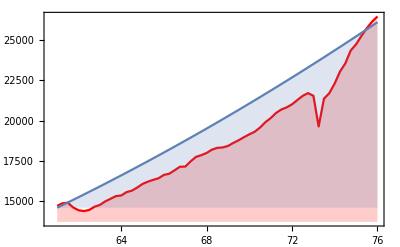
-Graphics-Gross Domestic Product ($)Time since 1947 (years)

```mathematica
Clear[maxX];
Clear[minX];
output=List@@@whole2;
whole3=Testrules;
output2=List@@@whole3;
model=a x+b x^2+c x^3+d x^4+e;
nlm=NonlinearModelFit[output,model,{a,b,c,d,e},x]
equation=Normal[nlm]
xValues=output2[[All,1]];
maxX=Max[xValues];
minX=Min[xValues];
(*Show[ListPlot[output2,PlotStyle->Red],Plot[nlm[x],{x,minX,maxX}],Frame->True,PlotStyle->Blue]*)
plotofmethod=Plot[nlm[x],{x,minX,maxX},Filling->Axis];
plotoftests=ListLinePlot[output2,PlotStyle->Red,Filling->Axis];

Labeled[Show[plotoftests,plotofmethod,Frame->True,PlotStyle->Blue],{"Gross Domestic Product ($)","Time since 1947 (years)"},{Left,Top},RotateLabel->True
]
```

## Using State Space Modeling

TimeSeriesModel[…]

SARIMAProcess[-159.593,{-0.413186},1,{0.60713,0.303489},{35,{},6,{}},505137.]

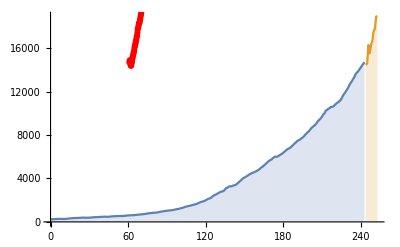
-Graphics-Gross Domestic Product ($)Time

```mathematica
output4=output;
output5=output2;
resultremovedfirstTrain=Map[Rest,output4];
resultremovedfirstTest=Map[Rest,output5];
improvedTrainresult=Flatten[resultremovedfirstTrain];
improvedTestresult=Flatten[resultremovedfirstTest];
tsm=TimeSeriesModelFit[improvedTrainresult]
normaltsm=Normal[tsm]
Labeled[Show[ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{10}]},Filling->Axis],ListPlot[output5,PlotStyle->Red]],{"Gross Domestic Product ($)","Time"},{Left,Top},RotateLabel->True
]
```

## Using Neural Networks

NetChain[<>]

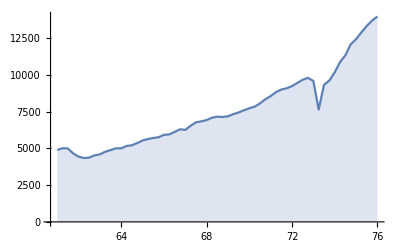
-Graphics-Gross Domestic Product ($)Error between the nueral net and test data

```mathematica
trainingData=Trainrules;
newKeyData=Keys[Testrules];
net=NetChain[{LinearLayer[10],Ramp,LinearLayer[1]}];
trainedNet=NetTrain[net,trainingData,LossFunction->MeanSquaredLossLayer[],Method->"ADAM",MaxTrainingRounds->10000,ValidationSet->Testrules]
testmodel={80,100,110,200};
trainedNet[testmodel];
NetPredictedValues=trainedNet[newKeyData];
graphicalrepnet=Thread[newKeyData->NetPredictedValues];
TestrulesNeccessaryState=Map[List,Testrules];
TestrulesNeccessaryalpha=Flatten[TestrulesNeccessaryState,1];
ErrorPresentedbetween=MapThread[#1[[1]]->(#1[[2]]-#2[[2]])&,{graphicalrepnet,TestrulesNeccessaryalpha}];
NegativeErrorPresentedbetween=Map[#1[[1]]->-#1[[2]]&,ErrorPresentedbetween];
Labeled[ListLinePlot[NegativeErrorPresentedbetween/. Rule->List,Filling->Axis],{"Gross Domestic Product ($)","Error between the nueral net and test data"},{Left,Top},RotateLabel->True
]
```

## Estimated Errors and their Implications

By a manual computation these are the estimated error areas of each model :

Non-linear model fit: The estimated area of the blue region is approximately 140,000 square units.

State Space Model: The estimated area between the red line and the blue line is approximately 2,300,000 square units.

Neural Net: The estimated area between the blue line and the x-axis is approximately 112,000 square units.

Based on the above results, we could conclude that on a limited amount of data a neural net would be the most appropriate simple model to use to make predictions on limited data.

## Limitations

Some limitations of the results include:

The existence of a limited amount of data may give rise to a circumstance wherein one method appears comparatively more appropriate than another.

The complexity of each algorithm may make one model better than the other and the complexity was not used as a quality indicator here.

Each model necessitated varying degrees of data cleaning; for instance, manipulating date objects in state space modeling was simpler, and the utilization of relative time was unnecessary.

It is worth noting that the simplicity of each model constituted a limitation to their predictive power.